# PHAS2443: Practical Mathematics II Exercises 4: Time-Dependent Problems

1. We saw in Lecture 3 that the forward Euler method is not very good at preserving the energy in a simulation of a Simple Harmonic Oscillator problem. This exercise compares the behaviour of that algorithm with two algorithms of the kind introduced by Verlet. There are three commonly-used forms of Verlet algorithm: we consider a particle of unit mass moving in one dimension under the influence of a force F(x), and integrate with a constant time-step Δt:
  a) Simple Verlet
         x(t+Δt) = 2 x(t) - x(t-Δt) + Δt^2 F(x(t)),
         with the velocity at time t calculated as
         v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt).

Simulating motion of particle in a simple harmonic oscillator
F = kx = m a
k = 1, m = 1
t_max = 100
δt = 1
x[0] = 1
v[0] = 0

```mathematica
Clear[simpleVerleter, simpleLister, energy]

simpleVerleter[list_, δt_, tmax_] := 
NestList[

{
2 #[[1]] - #[[2]] + (δt^2) (-#[[1]]),                               (* x(t + δt) =  2x(t) - x(t - δt) + δt^2 F(x(t)) *)
#[[1]],                                                                                                       (* the last value of x                             *)
((2 #[[1]] - #[[2]] + (δt^2) (-#[[1]])) - #[[2]]) / (2 δt) (* v(t) = (x(t + δt) - x(t - δt))/(2δt)                         *)
} &,

list,  (* pass this to the pure function *)
Floor[tmax/δt] (* calculates how many times to NestList *)
] 

simpleLister[list_, δt_, tmax_] := (* extracting a list of {x, vel} from simpleVerleter *)
Drop[Transpose[Drop[Transpose[simpleVerleter[list, δt, tmax]], {2}]] ,1]

energy[list_, δt_, tmax_] := (* E = (x^2  + v^2)/2; passing a pure function of this to a verletLister list*)
(((#[[1]]^2 + #[[2]]^2) /2) & /@ verletLister[list, δt, tmax])- 0.5
```

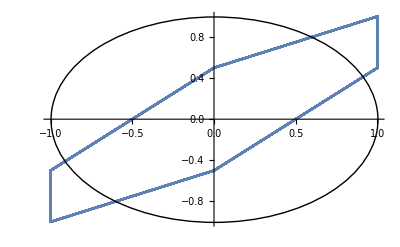

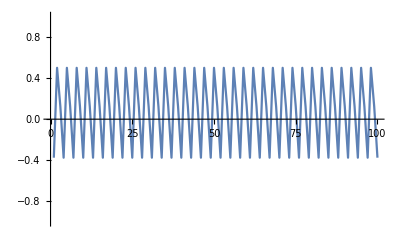

```mathematica
simplePlot1 = ListPlot[verletLister[{1,1,0}, 1, 100], Joined -> True];
circle = Graphics[Circle[]];

Show[simplePlot1, circle]


ListPlot[energy[{1,1,0}, 1, 100], Joined -> True, PlotRange-> {-1,1}]
```

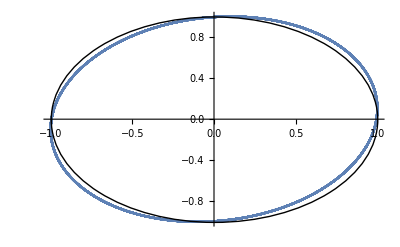

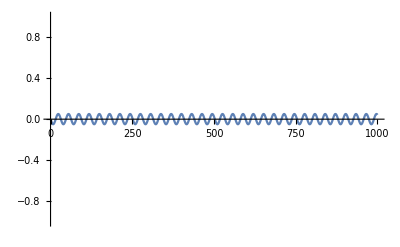

```mathematica
simplePlot01  = ListPlot[verletLister[{1,1,0}, 0.1, 100], Joined -> True];

Show[simplePlot01, circle]
ListPlot[energy[{1,1,0}, 0.1, 100], Joined -> True, PlotRange->{-1,1}]
```

b) Leap-Frog Verlet
        This introduces the velocities at half-time-steps
        v(t+Δ t/2) = v(t-Δ t/2) + Δ t F(x(t)),
        x(t+Δ t) = x(t) + Δ t  v(t+Δ t/2),
        and then if the velocity at t is needed it is estimated from
        v(t)=(v(t+Δt/2) + v(t-Δt/2))/2.

```mathematica
Clear[leapVerleter,leapLister]

leapVerleter[list_List, δt_, tmax_] :=  
NestList[

{
#[[1]] + δt (#[[4]] + δt (-#[[1]])) ,
#[[1]],
#[[4]] + (δt (-#[[1]]) / 2),
#[[3]]
} &,

list,  (* pass this to the pure function *)
Floor[tmax/δt] (* calculates how many times to NestList *)
] 

leapLister[list_, δt_, tmax_] := (* extracting a list of {x, vel} from simpleVerleter *)
Drop[Transpose[Drop[Transpose[leapVerleter[list, δt, tmax]], {2,4,2}]] ,1]
```

{{0,-1/2},{0,0},{-1/2,-1/2},{0,1/4},{-1/2,-1/2},{1/4,1/2},{-1/2,-5/8},{1/2,3/4},{-5/8,-7/8},{3/4,17/16}}

Part::partw: Part 4 of {1,1,0} does not exist.

```mathematica
leapPlot12= ListPlot[verletLister[{1,1,0}, 1, 100], Joined -> True];
circle = Graphics[Circle[]];

Show[leapPlot1, circle]
```

c) velocity-Verlet
        uses the definition
        v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt)
        to evaluate velocities and positions at the same times:
           x(t+Δ t) = x(t) + Δ t  v(t) +(Δ t)^2 F(x(t))/2,
          v(t+Δ t) = v(t) + Δ t [F(x(t+Δ t))+F(x(t))]/2.
       Write code to implement algorithms a), b) and c), and apply them to solve the simple harmonic oscillator problem for a unit mass on the end of a spring with spring constant unity, starting at rest with a displacement of 1. In each case plot i) the phase diagram, with position along the x-axis and velocity up the y-axis, with the unit circle drawn to illustrate the ideal result, ii) the difference between the total energy (v^2 + x^2)/2 and the exact energy, 0.5. In each case integrate up to a time of 100, with a timestep of 1 and with a timestep of 0.1.
       You may find it useful to keep, at each step, a list of values such as {x, xlast,vel} and to write the update in a form such as update[{x,xlast,vel}]:={(function of x, xlast, vel), x, (function of x, xlast, vel)} -- if you think back to our functions for the Fibonacci numbers in PHAS1449, or Newton's method in lecture 1 of this course, you will find similar expressions. If you are at all confused about the order in which things will get evaluated, you might find it easier to write a Module.

2. This question is one that requires pencil and paper rather than programming. It is concerned with the consistency of finite difference schemes.
  If we try to solve the equation
  (∂y)/(∂t)=(∂^2 y)/(∂x^2)
  with the simplest scheme we can think of, we might use a centred difference scheme for the time derivative and a standard scheme for the spatial second derivative. With x→i Δx and t→n Δt this gives
  (y(i,n+1)-y(i,n-1))/(2 Δt)= (y(i-1,n)-2y(i,n)+y(i+1,n))/(Δx)^2.
  Unfortunately, this scheme is unstable. Maybe it is possible to make it stable by inserting values of y at different times on the right-hand side. A fairly general way of doing this is to write
   (y(i,n+1)-y(i,n-1))/(2 Δt)= (y(i-1,n)-2[θ y(i,n+1) + (1-θ) y(i,n-1)]+y(i+1,n))/(Δx)^2.
   Investigate the consistency of this scheme as Δx tends to zero if:
   i) Δt = r Δ x
   ii) Δt = r (Δx)^2
   where r is a positive constant, and θ may take any value between 0 and 1.

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.